```mathematica
Многочлены Лагранжа
```

```mathematica
y=x^2
```

```mathematica
fn1="D:\\5 семестр\\Методы вычислений\\LR_4\\LR_4\\sRender_Grid\\fun1.txt";
file1=OpenRead[fn1];
f1x={};f1y={};
temp=Read[file1,{Number,Number}];
end=ToString@EndOfFile;
While[ToString@temp≠end,
AppendTo[f1x,temp[[1]]];
AppendTo[f1y,temp[[2]]];
temp=Read[file1,{Number,Number}]]
```

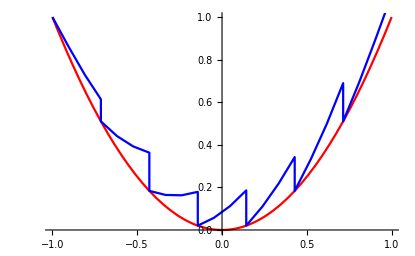

```mathematica
Show[Plot[x^2,{x,-1,1},PlotStyle->Red],ListLinePlot[Transpose[{f1x,f1y}],PlotStyle->Blue]]
```

```mathematica
(2/3+2/3) 2//N
```

2.66667

```mathematica
-1.667 1.065-0.667 0.547+1.065
```

-1.0752

```mathematica
Exp[-1.71429]//N
```

0.180092

```mathematica
y=1/(1+x^2)
```

```mathematica
fn2="D:\\5 семестр\\Методы вычислений\\LR_4\\LR_4\\Render_Grid\\fun2.txt";
file2=OpenRead[fn2];
f2x={};f2y={};
temp=Read[file2,{Number,Number}];
end=ToString@EndOfFile;
While[ToString@temp≠end,
AppendTo[f2x,temp[[1]]];
AppendTo[f2y,temp[[2]]];
temp=Read[file2,{Number,Number}]]
```

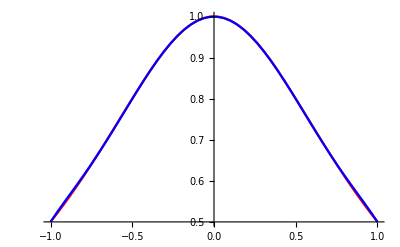

```mathematica
Show[Plot[1/(1+x^2),{x,-1,1},PlotStyle->Red],ListLinePlot[Transpose[{f2x,f2y}],PlotStyle->Blue]]
```

```mathematica
y=1/ArcTan[1+10 x^2]
```

```mathematica
fn3="D:\\5 семестр\\Методы вычислений\\LR_4\\LR_4\\Render_Grid\\fun3.txt";
file3=OpenRead[fn3];
f3x={};f3y={};
temp=Read[file3,{Number,Number}];
end=ToString@EndOfFile;
While[ToString@temp≠end,
AppendTo[f3x,temp[[1]]];
AppendTo[f3y,temp[[2]]];
temp=Read[file3,{Number,Number}]]
```

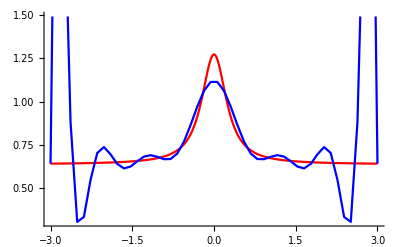

```mathematica
Show[Plot[1/ArcTan[1+10 x^2],{x,-3,3},PlotStyle->Red,PlotRange->All],ListLinePlot[Transpose[{f3x,f3y}],PlotStyle->Blue]]
```

```mathematica
Sin[(x^4+x^3-3x+3-30^(1/3))/2]+Tanh[(4*√3 x^3-2 x-6 √2+1)/(-2 √3 x^3+x+3 √2)]+1.2
```

```mathematica
fn5="D:\\5 семестр\\Методы вычислений\\LR_4\\LR_4\\Render_Grid\\fun5.txt";
file5=OpenRead[fn5];
f5x={};f5y={};
temp=Read[file5,{Number,Number}];
end=ToString@EndOfFile;
While[ToString@temp≠end,
AppendTo[f5x,temp[[1]]];
AppendTo[f5y,temp[[2]]];
temp=Read[file5,{Number,Number}]]
```

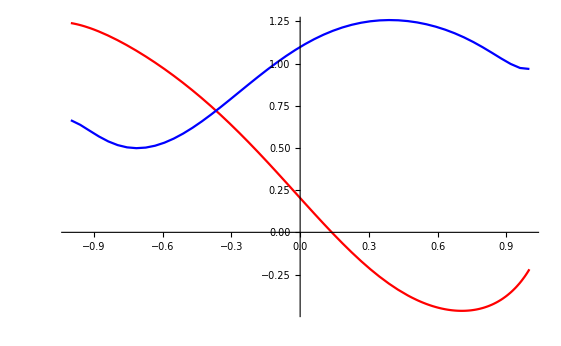

```mathematica
Show[Plot[Sin[(x^4+x^3-3x+3-30^(1/3))/2]+Tanh[(4 √3 x^3-2 x-6 √2+1)/(-2 √3 x^3+x+3 √2)]+1.2,{x,-1,1},PlotStyle->Red],ListLinePlot[Transpose[{f5x,f5y}],PlotStyle->Blue]]
```

```mathematica
fn6="D:\\5 семестр\\Методы вычислений\\LR_4\\LR_4\\sRender_Grid\\fun6.txt";
file6=OpenRead[fn6];
f6x={};f6y={};
temp=Read[file6,{Number,Number}];
end=ToString@EndOfFile;
While[ToString@temp≠end,
AppendTo[f6x,temp[[1]]];
AppendTo[f6y,temp[[2]]];
temp=Read[file6,{Number,Number}]]
```

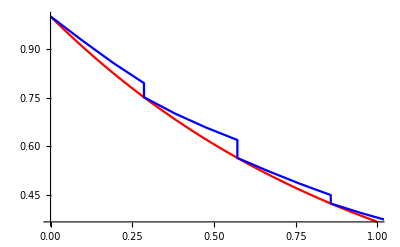

```mathematica
Show[Plot[Exp[-x],{x,0,1},PlotStyle->Red],ListLinePlot[Transpose[{f6x,f6y}],PlotStyle->Blue]]
```